## Fixed M_Z'=10 TeV, Fixed Brane parameter = 0.2, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL02=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.2)
```

0.199871

```mathematica
Zprime10decayfixedmass02[CvR_]:=MassZprime10/(12π)(1/4(CvL02+CvR)^2+1/4(CvL02-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL02+CvR)^2-1/2(CvL02+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
```

```mathematica
Zprime10decayfixedmass02[0.0]
Zprime10decayfixedmass02[0.1]
Zprime10decayfixedmass02[0.2]
Zprime10decayfixedmass02[0.3]
Zprime10decayfixedmass02[0.4]
Zprime10decayfixedmass02[0.5]
Zprime10decayfixedmass02[0.6]
Zprime10decayfixedmass02[0.7]
Zprime10decayfixedmass02[0.8]
Zprime10decayfixedmass02[0.9]
Zprime10decayfixedmass02[1.0]
```

5.29674

6.6221

10.5992

17.2282

26.5089

38.4414

53.0257

70.2618

90.1497

112.689

137.881

```mathematica
DecayTableFixed1002=TableForm[{{0.0,Zprime10decayfixedmass02[0.0]},{0.1,Zprime10decayfixedmass02[0.1]},{0.2,Zprime10decayfixedmass02[0.2]},{0.3,Zprime10decayfixedmass02[0.3]},{0.4,Zprime10decayfixedmass02[0.4]},{0.5,Zprime10decayfixedmass02[0.5]},{0.6,Zprime10decayfixedmass02[0.6]},{0.7,Zprime10decayfixedmass02[0.7]},{0.8,Zprime10decayfixedmass02[0.8]},{0.9,Zprime10decayfixedmass02[0.9]},{1.0,Zprime10decayfixedmass02[1.0]}},TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 5.29674
0.1 | 6.6221
0.2 | 10.5992
0.3 | 17.2282
0.4 | 26.5089
0.5 | 38.4414
0.6 | 53.0257
0.7 | 70.2618
0.8 | 90.1497
0.9 | 112.689
1. | 137.881

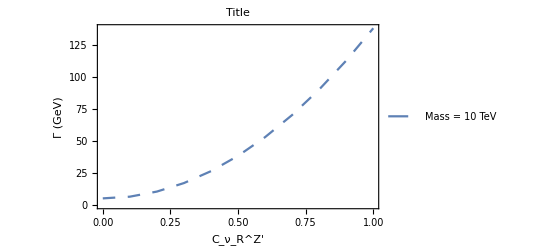

```mathematica
PlotZprimeDecayFixed1002=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

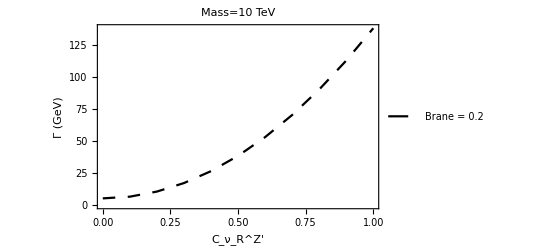

```mathematica
PlotZprimeDecayFixed1002B=ListPlot[%%, Joined-> True,PlotStyle->{Black,Dashing[Medium]},PlotLegends->{"Brane = 0.2"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 0.2, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL02=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.2)
```

0.199871

```mathematica
Zprime8decayfixedmass02[CvR_]:=MassZprime8/(12π)(1/4(CvL02+CvR)^2+1/4(CvL02-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL02+CvR)^2-1/2(CvL02+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
```

```mathematica
Zprime8decayfixedmass02[0.0]
Zprime8decayfixedmass02[0.1]
Zprime8decayfixedmass02[0.2]
Zprime8decayfixedmass02[0.3]
Zprime8decayfixedmass02[0.4]
Zprime8decayfixedmass02[0.5]
Zprime8decayfixedmass02[0.6]
Zprime8decayfixedmass02[0.7]
Zprime8decayfixedmass02[0.8]
Zprime8decayfixedmass02[0.9]
Zprime8decayfixedmass02[1.0]
```

4.23667

5.29655

8.47749

13.7795

21.2026

30.7468

42.412

56.1983

72.1057

90.1341

110.284

```mathematica
DecayTableFixed802=TableForm[{{0.0,Zprime8decayfixedmass02[0.0]},{0.1,Zprime8decayfixedmass02[0.1]},{0.2,Zprime8decayfixedmass02[0.2]},{0.3,Zprime8decayfixedmass02[0.3]},{0.4,Zprime8decayfixedmass02[0.4]},{0.5,Zprime8decayfixedmass02[0.5]},{0.6,Zprime8decayfixedmass02[0.6]},{0.7,Zprime8decayfixedmass02[0.7]},{0.8,Zprime8decayfixedmass02[0.8]},{0.9,Zprime8decayfixedmass02[0.9]},{1.0,Zprime8decayfixedmass02[1.0]}},TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 4.23667
0.1 | 5.29655
0.2 | 8.47749
0.3 | 13.7795
0.4 | 21.2026
0.5 | 30.7468
0.6 | 42.412
0.7 | 56.1983
0.8 | 72.1057
0.9 | 90.1341
1. | 110.284

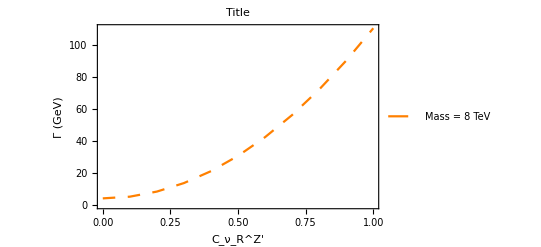

```mathematica
PlotZprimeDecayFixed802=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

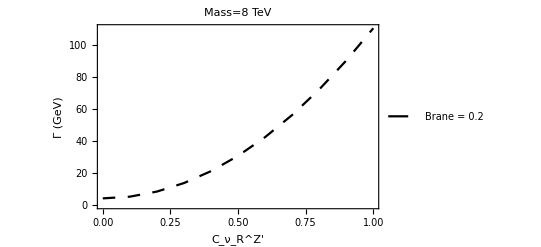

```mathematica
PlotZprimeDecayFixed802B=ListPlot[%%, Joined-> True,PlotStyle->{Black,Dashing[Medium]},PlotLegends->{"Brane = 0.2"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 0.2, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL02=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(0.2)
```

0.199871

```mathematica
Zprime5decayfixedmass02[CvR_]:=MassZprime5/(12π)(1/4(CvL02+CvR)^2+1/4(CvL02-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL02+CvR)^2-1/2(CvL02+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
```

```mathematica
Zprime5decayfixedmass02[0.0]
Zprime5decayfixedmass02[0.1]
Zprime5decayfixedmass02[0.2]
Zprime5decayfixedmass02[0.3]
Zprime5decayfixedmass02[0.4]
Zprime5decayfixedmass02[0.5]
Zprime5decayfixedmass02[0.6]
Zprime5decayfixedmass02[0.7]
Zprime5decayfixedmass02[0.8]
Zprime5decayfixedmass02[0.9]
Zprime5decayfixedmass02[1.0]
```

2.64598

3.30727

5.29326

8.60395

13.2393

19.1994

26.4842

35.0937

45.0279

56.2868

68.8704

```mathematica
DecayTableFixed502=TableForm[{{0.0,Zprime5decayfixedmass02[0.0]},{0.1,Zprime5decayfixedmass02[0.1]},{0.2,Zprime5decayfixedmass02[0.2]},{0.3,Zprime5decayfixedmass02[0.3]},{0.4,Zprime5decayfixedmass02[0.4]},{0.5,Zprime5decayfixedmass02[0.5]},{0.6,Zprime5decayfixedmass02[0.6]},{0.7,Zprime5decayfixedmass02[0.7]},{0.8,Zprime5decayfixedmass02[0.8]},{0.9,Zprime5decayfixedmass02[0.9]},{1.0,Zprime5decayfixedmass02[1.0]}},TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 2.64598
0.1 | 3.30727
0.2 | 5.29326
0.3 | 8.60395
0.4 | 13.2393
0.5 | 19.1994
0.6 | 26.4842
0.7 | 35.0937
0.8 | 45.0279
0.9 | 56.2868
1. | 68.8704

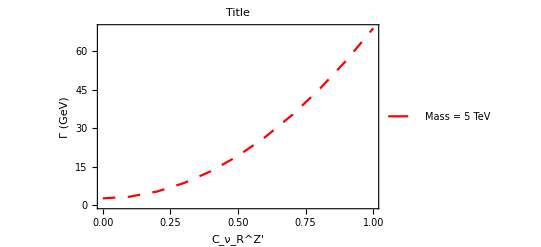

```mathematica
PlotZprimeDecayFixed502=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Title],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

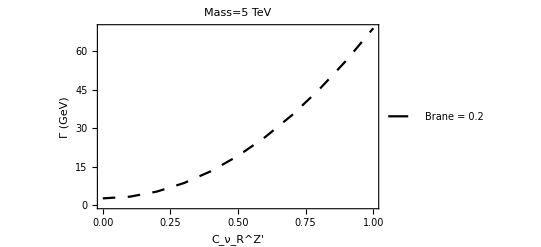

```mathematica
PlotZprimeDecayFixed502B=ListPlot[%%, Joined-> True,PlotStyle->{Black,Dashing[Medium]},PlotLegends->{"Brane = 0.2"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

## OverLay

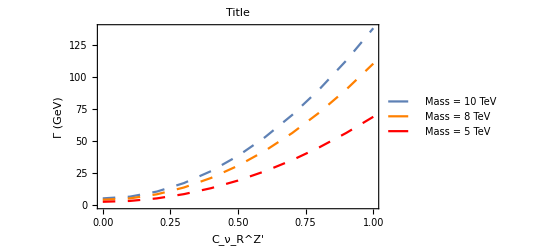

```mathematica
Show[PlotZprimeDecayFixed1002,PlotZprimeDecayFixed802,PlotZprimeDecayFixed502]
```

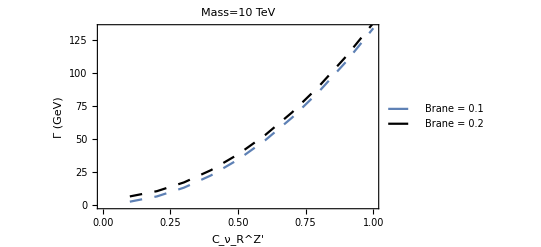

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B]
```

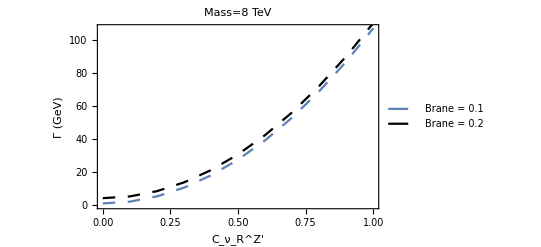

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B]
```

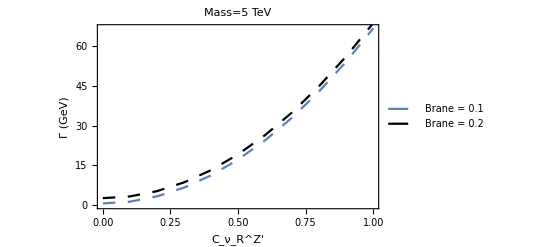

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B]
```